# Gurney 83 à 2 stades de développement, cohort competition

## Comparaison délai fixe - délai distribué

## Système DDE

## Définition du système

### Forme du système avec stades explicites

```mathematica
systemDDE = {
J'[t] == q A[t] Exp[-A[t]/A0] - q A[t- τ1] Exp[-A[t-τ1]/A0] Exp[-δj τ1] - δj J[t], 
A'[t] == q A[t-τ1 ]Exp[-A[t-τ1]/A0] Exp[-δj τ1]  - δa A[t]}
```

{J'[t]==ⅇ^(-A[t]/A0) q A[t]-ⅇ^(-δj τ1-A[t-τ1]/A0) q A[t-τ1]-δj J[t],A'[t]==-δa A[t]+ⅇ^(-δj τ1-A[t-τ1]/A0) q A[t-τ1]}

```mathematica
qq=8.5;
δaq=0.27;
δjq=0.07;
τ1q=0.6;
A0q=600;
```

### Forme minimal du système

```mathematica
SystemMinDDE = q  Exp[-τ1 δj] A[t - τ1] Exp[-A[t-τ1]/A0]-δa A[t]
```

-δa A[t]+ⅇ^(-δj τ1-A[t-τ1]/A0) q A[t-τ1]

## Équation du système à l’équilibre

```mathematica
systemEqDDE = q  Exp[-τ1 δj] Aeq Exp[-Aeq/A0]-δa Aeq
systemEq2DDE= {
q A Exp[-A/A0] - q A Exp[-A/A0] Exp[-δj τ1] - δj J, 
 q A Exp[-A/A0] Exp[-δj τ1]  - δa A}
```

Aeq ⅇ^(-Aeq/A0-δj τ1) q-Aeq δa

{A ⅇ^(-A/A0) q-A ⅇ^(-A/A0-δj τ1) q-J δj,A ⅇ^(-A/A0-δj τ1) q-A δa}

## Expression des Points Fixes

```mathematica
SolEqDDE = Solve[systemEqDDE==0, {Aeq}] //FullSimplify
```

Solve::ifun: Inverse functions are being used by Solve, so some solutions may not be found; use Reduce for complete solution information.

{{Aeq→0},{Aeq→-A0 (δj τ1+Log[δa/q])}}

```mathematica
SolEqDDE2 = Solve[systemEq2DDE==0, {J,A}] //FullSimplify
```

Solve::incnst: Inconsistent or redundant transcendental equation. After reduction, the bad equation is InverseFunction[#1 ⅇ^#1&,1,1][-(A ⅇ^(-A/A0))/A0] == 0.

Solve::incnst: Inconsistent or redundant transcendental equation. After reduction, the bad equation is -δj τ1-Log[δa/q]+InverseFunction[#1 ⅇ^#1&,1,1][-(A ⅇ^(-A/A0))/A0] == 0.

Solve::ifun: Inverse functions are being used by Solve, so some solutions may not be found; use Reduce for complete solution information.

{{J→0,A→0},{J→-(A0 (-1+ⅇ^(δj τ1)) δa (δj τ1+Log[δa/q]))/δj,A→-A0 (δj τ1+Log[δa/q])}}

```mathematica
AnnTriDDE = Aeq/.SolEqDDE[[2]][[1]]
ATriDDE  = Aeq/.SolEqDDE[[1]] [[1]]
```

-A0 (δj τ1+Log[δa/q])

0

#### Condition d’existence du Point Fixe non trivial

Ce point fixe est dans les réels positifs si q > δa Exp[δj τ1]

```mathematica
Solve[q==δa Exp[δj τ1], δa]
CondEx = δa < q Exp[-δj τ1]
CondInex = δa > q Exp[-δj τ1]
daLimNT[t1_] := ⅇ^(-δj t1) q
```

{{δa→ⅇ^(-δj τ1) q}}

δa<ⅇ^(-δj τ1) q

δa>ⅇ^(-δj τ1) q

## Linéarisation

### Développement de Taylor d’ordre 1

```mathematica
DLDDE = D[q  Exp[-τ1 δj] A[t - τ1] Exp[-A[t-τ1]/A0],A[t-τ1]]//FullSimplify;
DLDDE= DLDDE/.{A[t-τ1]-> Aeq};
DLDDE = nA'[t]==DLDDE * nA[t-τ1] - δa nA[t]
```

nA'[t]==-δa nA[t]+((A0-Aeq) ⅇ^(-(Aeq+A0 δj τ1)/A0) q nA[t-τ1])/A0

## Transformé de Laplace

```mathematica
EqLaplaceDDE = DLDDE /.{nA'[t]->s LnA[s],nA[t-τ1]->LnA[s] Exp[-s τ1],nA[t]->LnA[s]}
```

s LnA[s]==((A0-Aeq) ⅇ^(-s τ1-(Aeq+A0 δj τ1)/A0) q LnA[s])/A0-δa LnA[s]

## Équations caractéristiques

### Équation caractéristique Point Fixe trivial

```mathematica
eqCaraTriDDE = D[EqLaplaceDDE/.{Aeq -> ATri},LnA[s]]
```

s==((A0-ATri) ⅇ^(-s τ1-(ATri+A0 δj τ1)/A0) q)/A0-δa

```mathematica
VPTriDDE = Solve[eqCaraTriDDE,s]
```

Solve::ifun: Inverse functions are being used by Solve, so some solutions may not be found; use Reduce for complete solution information.

{{s→(-δa τ1+ProductLog[((A0-ATri) ⅇ^(-ATri/A0+δa τ1-δj τ1) q τ1)/A0])/τ1}}

```mathematica
Solve[δa τ1==ProductLog[ⅇ^(δa τ1-δj τ1) q τ1],q]
```

{{q→ⅇ^(δj τ1) δa}}

ProductLog[ⅇ^(δa τ1-δj τ1) q τ1] est croissant sur q 
On voit que le point fixe trivial à sa valeur propre supérieur à 0 pour q > ⅇ^(δj τ1) δa
Soit la condition d’existence du point fixe non trivial
Donc le point fixe trivial est instable pour les conditions d’existence du point fixe non trivial

### Équation caractéristique Point Fixe non trivial

```mathematica
eqCaraNonTriDDE = D[EqLaplaceDDE/.{Aeq -> AnnTriDDE},LnA[s]]//FullSimplify
```

s+δa==ⅇ^(-s τ1) δa (1+δj τ1+Log[δa/q])

```mathematica
VPNonTriDDE = Solve[eqCaraNonTriDDE,s]
```

Solve::ifun: Inverse functions are being used by Solve, so some solutions may not be found; use Reduce for complete solution information.

{{s→(-δa τ1+ProductLog[ⅇ^(δa τ1) δa τ1 (1+δj τ1+Log[δa/q])])/τ1}}

```mathematica
Solve[δa τ1==ProductLog[ⅇ^(δa τ1) δa τ1 (1+δj τ1+Log[δa/q])],q]
```

{{q→ⅇ^(δj τ1) δa}}

ProductLog[ⅇ^(δa τ1) δa τ1 (1+δj τ1+Log[δa/q])] est décroissant sur q
Ici, le point fixe non trivial à sa valeur propre inférieur à 0 pour q > ⅇ^(δj τ1) δa
Soit la condition d’existence du point fixe non trivial
Donc le point fixe non trivial est stable pour les conditions d’existence du point fixe non trivial

## Diagramme de stabilité fonction de δa et q (Gurney 1980)

Un jeu qui pourrait être celui utilisé dans Gurney 1980 pour les Blowflies (mais il n’est pas explicitement donné).

```mathematica
parGurney1980 = {δj -> .0,τ1->20, A0->600};
contour = ContourPlot[s/.VPNonTriDDE/.parGurney1980 //N // Re,
{δa, 0.01,10},{q, 1,1000},
ImageSize->{400,400},
AspectRatio-> 1,
Frame -> False,
Axes -> True,
AxesLabel-> {"δa", "q"},
Contours->{0},(*Trace la courbe Re(λ)=0*)
ContourStyle->{Thick,Black},
ColorFunction->(If[#>0,Purple,Yellow]&),
ColorFunctionScaling->False,
PlotLabel->"Régions de stabilité (jaune-stable)",
ScalingFunctions->{"Log","Log"}
];

RegionPlotEx = RegionPlot[CondInex/.parGurney1980, 
{δa, 0.01,10},{q, 1,1000},
ImageSize->{400,400},
AspectRatio-> 1,
Frame -> False,
Axes -> True,
AxesLabel-> {"δa", "τ1"},
ColorFunction->Hue,
ScalingFunctions->{"Log","Log"}
];

plotline = ListLinePlot[Table[{daval, 8.5}, {daval, 0.01,1.1,0.1}],
ImageSize->{400,400},
AspectRatio-> 1,
Frame -> False,
Axes -> True,
AxesLabel-> {"δa", "q"},
PlotStyle->{Dashed, Red},
ScalingFunctions->{"Log","Log"}
];

Show[contour,RegionPlotEx, plotline]
```

-Graphics-

Je comprends pas d’où vient la légère différence avec le graph du Gurney 1980 : τ1 mal estimé ?

Et pour des paramètres + liés à Gurney 1983 - Nicholson’s blowflies mais avec une mortalité juvénile boostée: (paramètres utilisés pour les graph τ1-δa)

```mathematica
parTableBlowflies = {δj -> 0.07,τ1->15.6, A0->600};
contour = ContourPlot[s/.VPNonTriDDE/.parTableBlowflies  //N // Re,
{δa, 0.01,10},{q, 1,1000},
ImageSize->{400,400},
AspectRatio-> 1,
Frame -> False,
Axes -> True,
AxesLabel-> {"δa", "q"},
Contours->{0},(*Trace la courbe Re(λ)=0*)
ContourStyle->{Thick,Black},
ColorFunction->(If[#>0,Purple,Yellow]&),
ColorFunctionScaling->False,
PlotLabel->"Régions de stabilité (jaune-stable)",
ScalingFunctions->{"Log","Log"}
];

RegionPlotEx = RegionPlot[CondInex/.parTableBlowflies, 
{δa, 0.01,10},{q, 1,1000},
ImageSize->{400,400},
AspectRatio-> 1,
Frame -> False,
Axes -> True,
AxesLabel-> {"δa", "τ1"},
ColorFunction->Hue,
ScalingFunctions->{"Log","Log"}
];

plotline = ListLinePlot[Table[{daval, 8.5}, {daval, 0.01,1.1,0.1}],
ImageSize->{400,400},
AspectRatio-> 1,
Frame -> False,
Axes -> True,
AxesLabel-> {"δa", "q"},
PlotStyle->{Dashed, Red},
ScalingFunctions->{"Log","Log"}
];

Show[contour, RegionPlotEx, plotline]
```

-Graphics-

NB : Pour s’y retrouver par rapport à l’autre type de diagramme où τ1 est en ordonnée : ici la ligne rouge  affichée correspond à la ligne rouge dans le graph plus bas.
δj non nul a un peu augmenté la zone de stabilité.

## Diagramme de stabilité fonction de δa et τ1

Un jeu qui pourrait être celui utilisé dans Gurney 1980 pour les Blowflies (mais il n’est pas explicitement donné).

Si δj=0, alors le signe de l’eq NT ne dépend plus de τ1. Pour que l’eq soit négatif, il faut alors seulement:

```mathematica
parGurney1980 = {δj -> .0,q->8.5, A0->600};
CondInex/.parGurney1980
```

δa>8.5

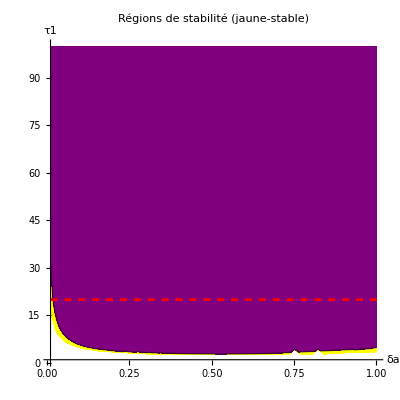

```mathematica
parGurney1980 = {δj -> .0,q->8.5, A0->600};
RegionPlotEx = RegionPlot[CondInex/.parGurney1980, 
{δa, 0, 1}, {τ1, 0, 100},
ImageSize->{400,400},
AspectRatio-> 1,
Frame -> False,
Axes -> True,
AxesLabel-> {"δa", "τ1"},
ColorFunction->Hue
];

StabPlot = ContourPlot[s/.VPNonTriDDE/.parGurney1980//N // Re,
{δa, 0.01,1},{τ1, 1,100},
ImageSize->{400,400},
AspectRatio-> 1,
Frame -> False,
Axes -> True,
AxesLabel-> {"δa", "τ1"},
Contours->{0},(*Trace la courbe Re(λ)=0*)
ContourStyle->{Thick,Black},
ColorFunction->(If[#>0,Purple,Yellow]&),
ColorFunctionScaling->False,
PlotLabel->"Régions de stabilité (jaune-stable)"
];

plotlinebis = ListLinePlot[Table[{daval, 20}, {daval, 0.01,10,0.5}],
ImageSize->{400,400},
AspectRatio-> 1,
Frame -> False,
Axes -> True,
AxesLabel-> {"δa", "q"},
PlotStyle->{Dashed, Red}
];

Show[StabPlot,RegionPlotEx, plotlinebis]
```

paramètres + liés à Gurney 1983 - Nicholson’s blowflies mais avec une mortalité juvénile boostée: (paramètres utilisés pour les graph τ1-δa)

```mathematica
parQuentin = {δj -> 0.07, A0->600, q->8.5};
stabcurveODE = ParametricPlot[{daLimNT[τ1]/.parQuentin,τ1 }, 
{τ1, 0.1,100},
PlotStyle->{Thick, Red},
ImageSize->{400,400},
AspectRatio-> 1,
Frame -> True,
PlotStyle->{Thick, Red},
FrameLabel -> {"δa", "τ1"},
PlotRange->{{0,1},{0,100}},
PlotStyle->{Thick, Red}
];

RegionPlotEx = RegionPlot[CondInex/.parQuentin, 
{δa, 0, 1}, {τ1, 0, 100},
ImageSize->{400,400},
AspectRatio-> 1,
Frame -> False,
Axes -> True,
AxesLabel-> {"δa", "τ1"},
ColorFunction->Hue
];

pts = {{0.8,80}, {0.4,30}, {0.2,10}};
ptslabel = {"A","B","C"};
StabPlot = ContourPlot[s/.VPNonTriDDE/.parQuentin //N // Re,
{δa, 0.01,1},{τ1, 1,100},
ImageSize->{400,400},
AspectRatio-> 1,
Frame -> False,
Axes -> True,
AxesLabel-> {"δa", "τ1"},
Contours->{0},(*Trace la courbe Re(λ)=0*)
ContourStyle->{Thick,Black},
ColorFunction->(If[#>0,Purple,Yellow]&),
ColorFunctionScaling->False,
PlotLabel->"Régions de stabilité (jaune-stable)",
Epilog->{PointSize[0.02],Black,Point[pts],Black}
];

plotlinebis = ListLinePlot[Table[{daval, 15.6}, {daval, 0.01,10,0.5}],
ImageSize->{400,400},
AspectRatio-> 1,
Frame -> False,
Axes -> True,
AxesLabel-> {"δa", "q"},
PlotStyle->{Dashed, Red}
];

Show[StabPlot,RegionPlotEx, plotlinebis]
```

-Graphics-

Bilan : 
	-δj nul -> zone instable beaucoup plus grande dans les deux types de diagramme : δj est stabilisant.
	-Une “patate”: à des couples (δa, τ1) intermédiaires, si δj stabilise assez autour, on a une brève zone d’instabilité.
	-Cette zone est étendue par q (cf diagrammes da-q avec le “V”). La fécondité est déstabilisante ici. La patate peut ainsi disparaître sous un certain seuil de fécondité.
		NB : Lucilia cuprina et Plodia ventura ont des fécondités qui permettent l’existence de la patate dans Gurney 1983. D’ailleurs, si on ignore le problème de la mortalité juvénile non estimée, ils se trouvent resp. en (0.27, 15.6) et en (0.2, 28) donc Lucilia dans la patate, Plodia hors de la patate.
			NB : de toute façon 1. on prend mal en compte δj (probablement plus faible en vrai donc on surestime la stabilité), et 2. Gurney1983 -> Compétition uniforme fit mieux la dynamique en labo de Plodia.

## Dynamiques (pour vérifier le dernier diagramme de stabilité)

```mathematica
pts = {{0.8,80}, {0.4,30}, {0.2,10}};
```

Vérifions les prédictions obtenues avec l’étude analytique. Utilisons le système minimal car autrement il y a de l’instabilité numérique et donne des choses bizarres.

```mathematica
systemMin= {
A'[t] == q A[t-τ1]Exp[-A[t-τ1]/A0] Exp[-δj τ1]  - δa A[t]};
tmax = 1000;
positions={AnnTriDDE, A0}
minMax={0,tmax};
```

{AnnTriDDE,A0}

{q→8.5,δa→0.8,δj→0.07,τ1→80,A0→600}

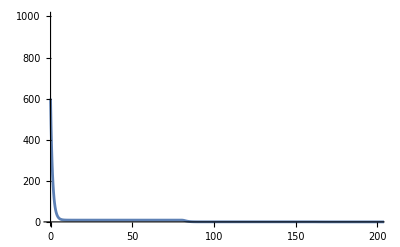

```mathematica
qq=8.5;
δaq=0.8;
δjq=0.07;
τ1q=80;
A0q=600;
par = {q->qq,δa ->δaq, δj -> δjq, τ1->τ1q, A0->A0q}

leqnIC=Flatten[{systemMin,{A[t/;t<=0]==A0q}}];
sol=NDSolve[leqnIC/. par,{A},{t,0,1000}];
Plot[A[t]/. sol[[1]]//Evaluate ,
{t,0,tmax},
PlotRange->{{0,200},{0,1000}}]
```

### Point de Quentin (vérifier qu’on est d’accord)

{q→8.5,δa→3/4,δj→0.07,τ1→80,A0→600}

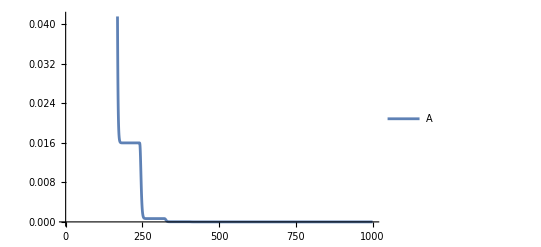

```mathematica
qq=8.5;
δaq=3/4;
δjq=0.07;
τ1q=80;
A0q=600;
par = {q->qq,δa ->δaq, δj -> δjq, τ1->τ1q, A0->A0q}

leqnIC=Flatten[{systemMin,{A[t/;t<=0]==A0q}}];
sol=NDSolve[leqnIC/. par,{A},{t,0,1000}];
Show[
Plot[A[t]/. sol[[1]]//Evaluate ,
{t,0,tmax},
PlotLegends->{"A"}],
Prolog->{Dashed,Thickness[0.005],Table[Line[{{minMax[[1]],x},{minMax[[2]],x}}],{x,positions/.par}]}
]
```

### Point de droite

{q→8.5,δa→0.8,δj→0.07,τ1→80,A0→600}

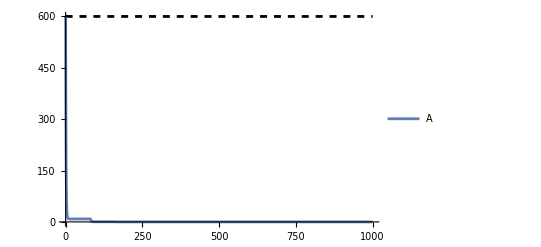

```mathematica
qq=8.5;
δaq=pts[[1,1]];
δjq=0.07;
τ1q=pts[[1,2]];
A0q=600;
par = {q->qq,δa ->δaq, δj -> δjq, τ1->τ1q, A0->A0q}

leqnIC=Flatten[{systemMin,{A[t/;t<=0]==A0q}}];
sol=NDSolve[leqnIC/. par,{A},{t,0,1000}];
Show[
Plot[A[t]/. sol[[1]]//Evaluate ,
{t,0,tmax},
PlotRange->{{0,tmax},{-1*positions[[1]]/.par,1*positions[[1]]/.par}},
PlotLegends->{"A"}],
Prolog->{Dashed,Thickness[0.005],Table[Line[{{minMax[[1]],x},{minMax[[2]],x}}],{x,positions/.par}]}
]
```

### Point au milieu

{q→8.5,δa→0.4,δj→0.07,τ1→30,A0→600}

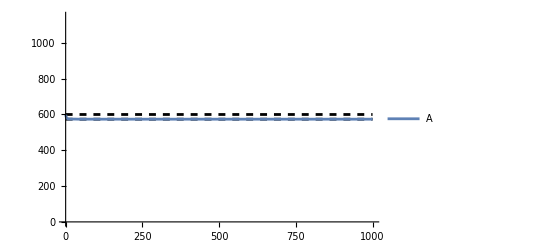

```mathematica
qq=8.5;
δaq=pts[[2,1]];
δjq=0.07;
τ1q=pts[[2,2]];
A0q=600;
par = {q->qq,δa ->δaq, δj -> δjq, τ1->τ1q, A0->A0q}

leqnIC=Flatten[{systemMin,{A[t/;t<=0]==A0q}}];
sol=NDSolve[leqnIC/. par,{A},{t,0,1000}];
Show[
Plot[A[t]/. sol[[1]]//Evaluate ,
{t,0,tmax},
PlotRange->{{0,tmax},{0,2*positions[[1]]/.par}},
PlotLegends->{"A"}],
Prolog->{Dashed,Thickness[0.005],Table[Line[{{minMax[[1]],x},{minMax[[2]],x}}],{x,positions/.par}]}
]
```

si on zoom A part bien de A0q et converge bien sur son équilibre

### Point à gauche

{q→8.5,δa→0.2,δj→0.07,τ1→10,A0→600}

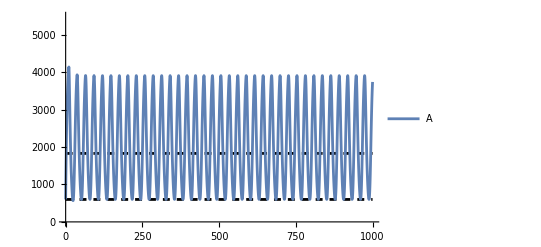

```mathematica
qq=8.5;
δaq=pts[[3,1]];
δjq=0.07;
τ1q=pts[[3,2]];
A0q=600;
par = {q->qq,δa ->δaq, δj -> δjq, τ1->τ1q, A0->A0q}

leqnIC=Flatten[{systemMin,{A[t/;t<=0]==A0q}}];
sol=NDSolve[leqnIC/. par,{A},{t,0,1000}];
Show[
Plot[A[t]/. sol[[1]]//Evaluate ,
{t,0,tmax},
PlotRange->{{0,tmax},{0,3*positions[[1]]/.par}},
PlotLegends->{"A"}],
Prolog->{Dashed,Thickness[0.005],Table[Line[{{minMax[[1]],x},{minMax[[2]],x}}],{x,positions/.par}]}
]
```

### Bilan

Les simulations sont cohérentes avec les résultats numériques trouvés sur le signe de la valeur propre.

## Diagramme de stabilité fonction de p_survie

```mathematica
parQuentin = {δj -> 0.07, A0->600, q->8.5};
replacement=Solve[1-pmort ==Exp[-δj τ1],τ1, Reals][[1]]//Normal;
VPNonTriDDEreplaced = VPNonTriDDE /.replacement;
ContourPlot[s/.VPNonTriDDEreplaced/.parQuentin //N // Re,
{δa, 0.01,1},{pmort,0.01,0.99},
ImageSize->{400,400},
AspectRatio-> 1,
Frame -> False,
Axes -> True,
AxesLabel-> {"δa", "1-p_survie"},
Contours->{0},(*Trace la courbe Re(λ)=0*)
ContourStyle->{Thick,Black},
ColorFunction->(If[#>0,Purple,Yellow]&),
ColorFunctionScaling->False,
PlotLabel->"Régions de stabilité (jaune-stable)",
Epilog->{PointSize[0.02],Black,Point[pts],Black}
]
```

-Graphics-

## Contourplot de p_survie sur le diagramme de stabilité original

```mathematica
parQuentin = {δj -> 0.07, A0->600, q->8.5};
psurvie = Exp[-δj τ1];
stabcurveODE = ParametricPlot[{daLimNT[τ1]/.parQuentin,τ1 }, 
{τ1, 0.1,100},
PlotStyle->{Thick, Red},
ImageSize->{400,400},
AspectRatio-> 1,
Frame -> True,
PlotStyle->{Thick, Red},
FrameLabel -> {"δa", "τ1"},
PlotRange->{{0,1},{0,100}},
PlotStyle->{Thick, Red}
];

RegionPlotEx = RegionPlot[CondInex/.parQuentin, 
{δa, 0, 1}, {τ1, 0, 100},
ImageSize->{400,400},
AspectRatio-> 1,
Frame -> False,
Axes -> True,
AxesLabel-> {"δa", "τ1"},
ColorFunction->Hue
];


psurvieplot = ContourPlot[psurvie/.parQuentin //N // Re,
{δa, 0.01,1},{τ1, 1,100},
ImageSize->{400,400},
AspectRatio-> 1,
Frame -> False,
Axes -> True,
AxesLabel-> {"δa", "τ1"},
ContourStyle->{Thick,Black}
];


Show[psurvieplot,RegionPlotEx]
```

-Graphics-

L’effet de la variab développementale sur p_survie ne suffira pas à expliquer l’apparitition et la taille de la patate (qui dépend de δa).

## Étude Analytique du système ODE

## Définition du système

### Forme du système avec stades explicites (obligé en contexte d’ODEs)

```mathematica
Declare[J,A,Real];
systemODE ={
J'[t] == q A[t] Exp[-A[t]/A0] - J[t]/τ1 - δj J[t], 
A'[t] == J[t]/τ1 - δa A[t]}
```

{J'[t]==ⅇ^(-A[t]/A0) q A[t]-δj (J[1][t]+J[2][t]+J[3][t]+J[4][t]+J[5][t]+J[6][t]+J[7][t]+J[8][t]+J[9][t]+J[10][t])-(J[1][t]+J[2][t]+J[3][t]+J[4][t]+J[5][t]+J[6][t]+J[7][t]+J[8][t]+J[9][t]+J[10][t])/τ1,A'[t]==-δa A[t]+(J[1][t]+J[2][t]+J[3][t]+J[4][t]+J[5][t]+J[6][t]+J[7][t]+J[8][t]+J[9][t]+J[10][t])/τ1}

## Expression des Points Fixes

```mathematica
SolEqODE = Solve[systemODE[[All,2]]=={0,0}, {J[t],A[t]},Reals] //FullSimplify // Normal
```

{{J[t]→0,A[t]→0},{J[t]→A0 δa τ1 Log[q/(δa+δa δj τ1)],A[t]→A0 Log[q/(δa+δa δj τ1)]}}

```mathematica
EqNonTriODE = SolEqODE[[2]] 
EqTriODE = SolEqODE[[1]]
```

{J[t]→A0 δa τ1 Log[q/(δa+δa δj τ1)],A[t]→A0 Log[q/(δa+δa δj τ1)]}

{J[t]→0,A[t]→0}

#### Condition d’existence du Point Fixe non trivial

Ce point fixe est dans les réels positifs si q > δa(1+δjτ1)

```mathematica
CondExODE =q>δa(1+δj τ1);
CondInexODE = q < δa(1+δj τ1);
LimEqODE[τ1_] := δa/.Solve[q==δa(1+δj τ1), δa][[1]]
```

## Jacobienne et équations caractéristiques

```mathematica
lJODE=D[systemODE[[All,2]],{{J[t], A[t]}}] ;
MatrixForm[lJODE]
```

(-δj-1/τ1 | ⅇ^(-A[t]/A0) q-(ⅇ^(-A[t]/A0) q A[t])/A0
1/τ1 | -δa)

### Équation caractéristique Point Fixe trivial

```mathematica
MatrixForm[lJODE/.EqTriODE]
```

(-δj-1/τ1 | q
1/τ1 | -δa)

```mathematica
polCaraTriODE =CharacteristicPolynomial[lJODE/.EqTriODE, x]
```

x^2+x δa+x δj+δa δj-q/τ1+x/τ1+δa/τ1

```mathematica
VPTriODE = Solve[polCaraTriODE == 0,x]
```

{{x→1/2 (-δa-δj-√((δa+δj+1/τ1)^2-4 (δa δj-q/τ1+δa/τ1))-1/τ1)},{x→1/2 (-δa-δj+√((δa+δj+1/τ1)^2-4 (δa δj-q/τ1+δa/τ1))-1/τ1)}}

```mathematica
Solve[-δa-δj-1/τ1==√((δa+δj+1/τ1)^2-4 (δa δj-q/τ1+δa/τ1)), q]
```

Solve::nongen: There may be values of the parameters for which some or all solutions are not valid.

{{q→δa+δa δj τ1}}

On voit que le point fixe trivial à sa valeur propre supérieur à 0 pour q >δa + δa δj τ1
Soit la condition d’existence du point fixe non trivial
Donc le point fixe trivial est instable pour les conditions d’existence du point fixe non trivial
(On peut aussi montrer que le déterminant et la trace ont le signe donné par la même inéquation que la cond d’existence de l’équilibre non trivial)

### Équation caractéristique Point Fixe non trivial

```mathematica
MatrixForm[lJODE/.EqNonTriODE]
```

(-δj-1/τ1 | δa+δa δj τ1-(δa+δa δj τ1) Log[q/(δa+δa δj τ1)]
1/τ1 | -δa)

```mathematica
polCaraNonTriODE =CharacteristicPolynomial[lJODE/.EqNonTriODE, x]
```

x^2+x δa+x δj+x/τ1+δa δj Log[q/(δa+δa δj τ1)]+(δa Log[q/(δa+δa δj τ1)])/τ1

```mathematica
VPNonTriODE = Solve[polCaraNonTriODE == 0,x]
```

{{x→1/2 (-δa-δj-1/τ1-√((δa+δj+1/τ1)^2-4 (δa δj Log[q/(δa+δa δj τ1)]+(δa Log[q/(δa+δa δj τ1)])/τ1)))},{x→1/2 (-δa-δj-1/τ1+√((δa+δj+1/τ1)^2-4 (δa δj Log[q/(δa+δa δj τ1)]+(δa Log[q/(δa+δa δj τ1)])/τ1)))}}

La première VP est négative pour tout paramètre. La deuxième VP est strictement positive quand -4 (δa δj Log[q/(δa+δa δj τ1)]+(δa Log[q/(δa+δa δj τ1)])/τ1) est strictement négatif ie quand le log est strictement négatif ie quand q < δa(1+δj τ1).
Donc l’équilibre non trivial est stable pour q>δa(1+δj τ1) : cela correspond à la condition d’existence d’un équilibre non trivial positif. Donc si l’équilibre non-trivial existe, il est stable.

### Même résultat attendu : utilisation de Routh Hurwitz (ordre 2)

```mathematica
{a2,a1,a0}=CoefficientList[polCaraNonTriODE,x];
```

```mathematica
critereMatrice = {a1>0,
a1*a2>0}
```

{δa+δj+1/τ1>0,(δa+δj+1/τ1) (δa δj Log[q/(δa+δa δj τ1)]+(δa Log[q/(δa+δa δj τ1)])/τ1)>0}

On vérifie déjà le premier critère si l’eq NT existe, et donc le deuxième critère est vérifié de la même manière que juste ci-dessus avec les VPs.

### Que donne Perron Frobenius (Plemmons 1977)?

On utilise N39 => J29 (Si N39 est vraie, J29: parties réelles de chaque valeur propre de -Jacobienne positive, donc négatives pour +Jacobienne, donc équilibre non trivial stable) 
N39 revient à un système de n inégalités. Il correspond à trouver x,y dans R*+ tq :
	-Jac(1,1)>Abs(-Jac(1,2))
	-Jac(2,2)>Abs(-Jac(2,1))
Donc ici ce système équivaut à:

```mathematica
PFcond = {-lJODE[[1,1]]>lJODE[[1,2]], -lJODE[[2,2]]>lJODE[[2,1]]}
```

{δj+1/τ1>ⅇ^(-A[t]/A0) q-(ⅇ^(-A[t]/A0) q A[t])/A0,δa>1/τ1}

```mathematica
PFcondeq = PFcond/.EqNonTriODE // FullSimplify
```

{δj+1/τ1+δa (1+δj τ1) (-1+Log[q/(δa+δa δj τ1)])>0,δa>1/τ1}

```mathematica
qq=8.5;
δaq=0.27;
δjq=0.07;
τ1q=0.6;
A0q=600;
par = {q->qq,δa ->δaq, δj -> δjq, τ1->τ1q, A0->A0q};
PFcondeq/.par
```

{True,False}

Ici on ne vérifie pas N39. Donc on ne peut rien conclure. J29 est peut-être vraie (elle l’est), mais l’implication ne permet pas de le démontrer.

## Étude Numérique

### Présentation rapide

Étude rapide de la partie imaginaire des valeurs propres pour différentes valeurs de τ1 et δa pour le point fixe non trivial

### Valeur des Paramètres fixés

Paramétrisation hasardeusement basée sur Gurney 83

```mathematica
qq=8.5;
δaq=0.27;
δjq=0.07;
τ1q=0.6;
A0q=600;
par = {q->qq,δa ->δaq, δj -> δjq, τ1->τ1q, A0->A0q};
```

### Vérification des conditions d’existence du PF non trivial

```mathematica
CondExODE /. par
```

True

Le point fixe non trivial existe bien pour les conditions testées, donc on a un équilibre stable non-nul.

## Diagramme de stabilité fonction de δa et q (cf Gurney 1980)

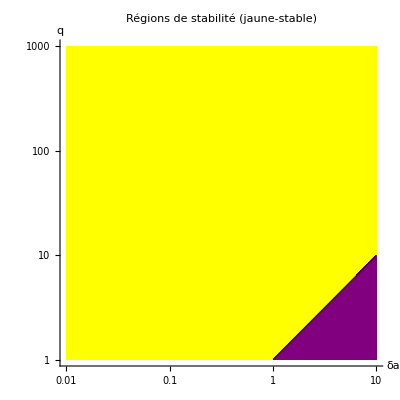

```mathematica
ContourPlot[x/.VPNonTriODE[[2]]/.{δj -> .0,τ1->20, A0->600} //N // Re,
{δa, 0.01,10},{q, 1,1000},
ImageSize->{400,400},
AspectRatio-> 1,
Frame -> False,
Axes -> True,
AxesLabel-> {"δa", "q"},
Contours->{0},(*Trace la courbe Re(λ)=0*)
ContourStyle->{Thick,Black},
ColorFunction->(If[#>0,Purple,Yellow]&),
ColorFunctionScaling->False,
PlotLabel->"Régions de stabilité (jaune-stable)",
ScalingFunctions->{"Log","Log"}
]
```

## Diagramme de stabilité fonction de δa et τ1

```mathematica
Solve[q==δa(1+δj τ1),δa]
```

{{δa→q/(1+δj τ1)}}

```mathematica
limeqODE[τ1_] := q/(1+δj τ1)
```

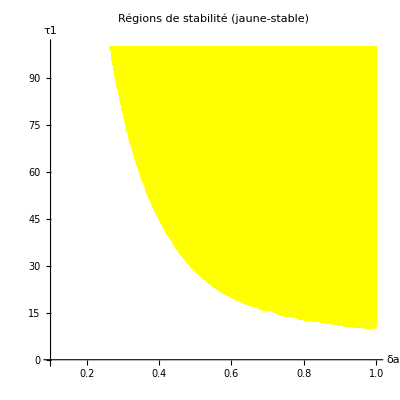

```mathematica
contourplotODE = ContourPlot[x/.VPNonTriODE[[2]]/.{q->qq, δj -> δjq, A0->A0q},
{δa, 0.1,1},{τ1, 0.1,100},
ImageSize->{400,400},
AspectRatio-> 1,
Frame -> False,
Axes -> True,
AxesLabel-> {"δa", "τ1"},
Contours->{0},(*Trace la courbe Re(λ)=0*)
ContourStyle->{Thick,Black},
ColorFunction->(If[#>0,Purple,Yellow]&),
ColorFunctionScaling->False,
PlotLabel->"Régions de stabilité (jaune-stable)"
];

stabcurveODE = ParametricPlot[{limeqODE[τ1]/.{q->qq, δj -> δjq, A0->A0q}, τ1}, 
{τ1, 0.1,100},
ImageSize->{400,400},
AspectRatio-> 1,
Frame -> True,
FrameTicks -> {{Automatic, None}, {Automatic, None}}, 
PlotLegends -> Automatic, 
FrameLabel -> {"δa", "τ1"},
PlotRange->{{0,1},{0,100}}
];

Show[contourplotODE, stabcurveODE]
```

```mathematica
contourplotODE = ContourPlot[x/.VPNonTriODE[[2]]/.{q->qq, δj -> δjq, A0->A0q},
{δa, 0.1,10},{τ1, 0.1,100},
ImageSize->{400,400},
AspectRatio-> 1,
Frame -> False,
Axes -> True,
AxesLabel-> {"δa", "τ1"},
Contours->{0},(*Trace la courbe Re(λ)=0*)
ContourStyle->{Thick,Black},
ColorFunction->(If[#>0,Purple,Yellow]&),
ColorFunctionScaling->False,
PlotLabel->"Régions de stabilité (jaune-stable)"
];

RegionPlotExODE = RegionPlot[CondInexODE/.{δj -> .07,q->8.5, A0->600}, 
{δa, 0, 10}, {τ1, 0, 100},
ImageSize->{400,400},
AspectRatio-> 1,
Frame -> False,
Axes -> True,
AxesLabel-> {"δa", "τ1"},
ColorFunction->Hue
];

stabcurveODE = ParametricPlot[{limeqODE[τ1]/.{q->qq, δj -> δjq, A0->A0q}, τ1}, 
{τ1, 0.1,100},
ImageSize->{400,400},
AspectRatio-> 1,
Frame -> True,
FrameTicks -> {{Automatic, None}, {Automatic, None}}, 
PlotLegends -> Automatic, 
PlotStyle->{Thick,Red},
FrameLabel -> {"δa", "τ1"},
PlotRange->{{0,10},{0,100}}
];

Show[contourplotODE, RegionPlotExODE,stabcurveODE]
```

-Graphics-

## Dynamiques

```mathematica
tmax = 500;
```

### Dans le blanc (stable et valeurs propres complexes)

-0.785+0.727273 ⅈ

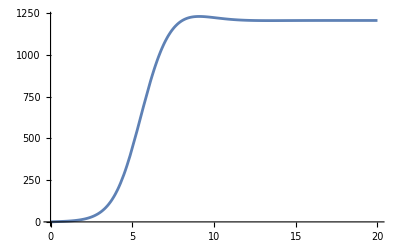

```mathematica
qq=8.5;
δaq=1;
δjq=0.07;
τ1q=2;
A0q=600;
par = {q->qq,δa ->δaq, δj -> δjq, τ1->τ1q, A0->A0q};
x/.VPNonTriODE[[2]]/.par

leqnICODE = Flatten[{systemODE, {J[0] == 10,A[0] == 0}}];
solODE=NDSolve[leqnICODE/.par, {J,A},{t, 0,tmax}];
Plot[Evaluate[A[t]/. solODE[[1]]],{t,0,20},
PlotRange->Full
]
```

### Dans le jaune (stable et valeurs propres réelles)

-0.0667971

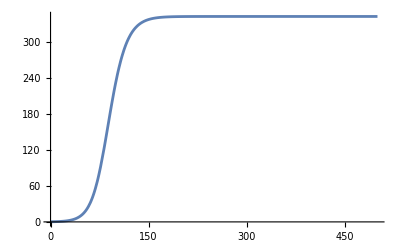

```mathematica
qq=8.5;
δaq=2;
δjq=0.07;
τ1q=20;
A0q=600;
par = {q->qq,δa ->δaq, δj -> δjq, τ1->τ1q, A0->A0q};
x/.VPNonTriODE[[2]]/.par

leqnICODE = Flatten[{systemODE, {J[0] == 10,A[0] == 0}}];
solODE=NDSolve[leqnICODE/.par, {J,A},{t, 0,tmax}];
Plot[Evaluate[A[t]/. solODE[[1]]],{t,0,tmax},
PlotRange->Full
]
```

### Dans le violet (instable mais équilibre négatif)

0.146528

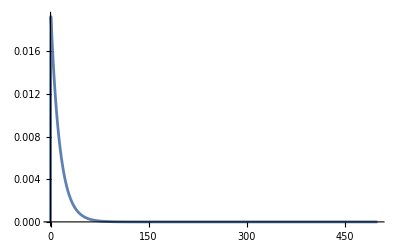

```mathematica
qq=8.5;
δaq=10;
δjq=0.07;
τ1q=50;
A0q=600;
par = {q->qq,δa ->δaq, δj -> δjq, τ1->τ1q, A0->A0q};
x/.VPNonTriODE[[2]]/.par

leqnICODE = Flatten[{systemODE, {J[0] == 10,A[0] == 0}}];
solODE=NDSolve[leqnICODE/.par, {J,A},{t, 0,tmax}];
Plot[Evaluate[A[t]/. solODE[[1]]],{t,0,tmax},
PlotRange->Full
]
```

## Conclusion pour ODE

Un équilibre non trivial toujours stable

## Étude Analytique du système LCT

## Définition du système

### Forme du système avec stades explicites

```mathematica
GenerateSystemLCT[nn_]:=Module[{eqns,i},eqns={};
(*Équations pour J[i]*)Do[AppendTo[eqns,D[J[i][t],t]==(-θ-δj) J[i][t]+If[i>1,θ J[i-1][t],q A[t] Exp[-A[t]/A0]]],{i,1,nn}];
(*Équation pour A*) AppendTo[eqns,D[A[t],t]==θ J[nn][t]-δa A[t]];
eqns];
```

```mathematica
nn = 8;
systemLCT = GenerateSystemLCT[nn]
```

{J[1]'[t]==ⅇ^(-A[t]/A0) q A[t]+(-δj-θ) J[1][t],J[2]'[t]==θ J[1][t]+(-δj-θ) J[2][t],J[3]'[t]==θ J[2][t]+(-δj-θ) J[3][t],J[4]'[t]==θ J[3][t]+(-δj-θ) J[4][t],J[5]'[t]==θ J[4][t]+(-δj-θ) J[5][t],J[6]'[t]==θ J[5][t]+(-δj-θ) J[6][t],J[7]'[t]==θ J[6][t]+(-δj-θ) J[7][t],J[8]'[t]==θ J[7][t]+(-δj-θ) J[8][t],A'[t]==-δa A[t]+θ J[8][t]}

## Expression des Points Fixes

à la main c’est bien plus simple (Mathematica gère mal la suite géometrique générée par les équations du LCT)
On obtient:

```mathematica
EqTriLCT = {J[t]->0, A[t]->0};

fJ = θ/(θ+δj);
αJ = ∑_(i=0)^(nn-1) (fJ)^(i-1);
AeqNonTri = A0*Log[q/δa(fJ)^n] // FullSimplify
JeqNonTri = AeqNonTri * δa/δj*(1-(fJ)^n)/fJ^n // FullSimplify
```

A0 Log[(q (θ/(δj+θ))^n)/δa]

-(A0 δa (θ/(δj+θ))^-n (-1+(θ/(δj+θ))^n) Log[(q (θ/(δj+θ))^n)/δa])/δj

#### Condition d’existence du Point Fixe non trivial

```mathematica
CondExLCT =q(fJ)^n > δa;
CondInexLCT =q(fJ)^n < δa;
Solve[q(fJ)^n == δa, δa]
LimEqLCT[τ1_] := δa/.Solve[q(fJ)^n == δa, δa][[1]];
```

{{δa→q (θ/(δj+θ))^n}}

```mathematica
LimEqLCT[1]
```

q (θ/(δj+θ))^n

## Jacobienne et équations caractéristiques

```mathematica
vars = Flatten[{Table[J[i][t],{i,1,nn}],A[t]}];
J[t] = Sum[J[i][t],{i,1,nn}];
varseq = Flatten[{Table[(JeqNonTri/αJ) fJ^(i-1),{i,1,nn}],AeqNonTri}];

lJLCT=D[systemLCT[[All,2]],{vars}] ;
MatrixForm[lJLCT]
```

(-δj-θ | 0 | 0 | 0 | 0 | 0 | 0 | 0 | ⅇ^(-A[t]/A0) q-(ⅇ^(-A[t]/A0) q A[t])/A0
θ | -δj-θ | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | θ | -δj-θ | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | θ | -δj-θ | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | θ | -δj-θ | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | θ | -δj-θ | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | θ | -δj-θ | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | θ | -δj-θ | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | θ | -δa)

### Point Fixe trivial

```mathematica
lJeqTriLCT=lJLCT /.
Thread[vars->Table[0,{i,1,nn+1}]];
MatrixForm[lJeqTriLCT] // FullSimplify 
polCaraTriLCT =CharacteristicPolynomial[lJeqTriLCT, x] ;
VPTriLCT = Solve[polCaraTriLCT == 0,x] ;
```

(-δj-θ | 0 | 0 | 0 | 0 | 0 | 0 | 0 | q
θ | -δj-θ | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | θ | -δj-θ | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | θ | -δj-θ | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | θ | -δj-θ | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | θ | -δj-θ | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | θ | -δj-θ | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | θ | -δj-θ | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | θ | -δa)

### Point Fixe non trivial

```mathematica
lJeqNonTriLCT=lJLCT /.
Thread[vars->varseq]// FullSimplify ;

MatrixForm[lJeqNonTriLCT]
```

(-δj-θ | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -δa (θ/(δj+θ))^-n (-1+Log[(q (θ/(δj+θ))^n)/δa])
θ | -δj-θ | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | θ | -δj-θ | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | θ | -δj-θ | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | θ | -δj-θ | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | θ | -δj-θ | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | θ | -δj-θ | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | θ | -δj-θ | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | θ | -δa)

```mathematica
polCaraNonTriLCT =CharacteristicPolynomial[lJeqNonTriLCT, x];
VPNonTriLCT = Solve[polCaraNonTriLCT == 0,x];
```

### Utilisation de Routh Hurwitz (ordre n+1)

à faire

```mathematica
{a2,a1,a0}=CoefficientList[polCaraNonTriODE,x];
```

```mathematica
critereMatrice = {a1>0,
a1*a2>0}
```

{δa+δj+1/τ1>0,(δa+δj+1/τ1) (δa δj Log[q/(δa+δa δj τ1)]+(δa Log[q/(δa+δa δj τ1)])/τ1)>0}

On vérifie déjà le premier critère si l’eq NT existe, et donc le deuxième critère est vérifié de la même manière que juste ci-dessus avec les VPs.

## Paramétrage

```mathematica
θ=n/τ1
```

n/τ1

## Étude Numérique

### Présentation rapide

Étude rapide de la partie imaginaire des valeurs propres pour différentes valeurs de τ1 et δa pour le point fixe non trivial

### Valeur des Paramètres fixés

Paramétrisation hasardeusement basée sur Gurney 83

```mathematica
qq=8.5;
δaq=0.27;
δjq=0.07;
τ1q=0.6;
A0q=600;
parLCT = {q->qq,δa ->δaq, δj -> δjq, τ1->τ1q, A0->A0q,n->nn};
parTable1 = {δj -> δjq,q->qq, A0->A0q};
parTable2 = {δj -> δjq,τ1->τ1q, A0->A0q};
```

### Vérification des conditions d’existence du PF non trivial

```mathematica
CondExLCT /. parLCT
```

True

Le point fixe non trivial existe bien pour les conditions testées.

## Diagramme de stabilité fonction de δa et q (cf Gurney 1980)

Un jeu qui pourrait être celui utilisé dans Gurney 1980 (mais il n’est pas explicitement donné).

```mathematica
parGurney1980 = {δj -> .0,τ1->20, A0->600};
VPMaxLCT2[daval_, qval_] := Eigenvalues[lJeqNonTriLCT/.{δa->daval, q->qval}/.parGurney1980/.{n->nn}] //Re // Max;
table2 = Table[{10^δalog, 10^qlog,VPMaxLCT2[10^δalog, 10^qlog]},{δalog, -2,1,0.1},{qlog, 0,3,0.1}];
table2flat = Flatten[table2,1]; (* Flatten first and second dimension -> have a list of triplets*)

plot = ListContourPlot[table2flat,
ImageSize->{400,400},
AspectRatio-> 1,
Frame->{{True,False},{True,False}},
Axes->False,
FrameLabel-> {"δa", "q"},
Contours->{0},(*Trace la courbe Re(λ)=0*)
ContourStyle->{Thick,Black},
ColorFunction->(If[#>0,Purple,Yellow]&),
ColorFunctionScaling->False,
PlotLabel->"Régions de stabilité (jaune-stable)",
ScalingFunctions->{"Log","Log"}
];

RegionPlotExLCT = RegionPlot[CondInexLCT/.parGurney1980/.n->nn, 
{δa, 0.01, 10}, {q, 1, 1000},
ImageSize->{400,400},
AspectRatio-> 1,
Frame->{{True,False},{True,False}},
Axes->False,
FrameLabel-> {"δa", "q"},
ColorFunction->Hue,
ScalingFunctions->{"Log","Log"}
];

Show[plot,RegionPlotExLCT]
```

-Graphics-

Et pour des paramètres + liés à Gurney 1983 - Nicholson’s blowflies mais avec une mortalité juvénile boostée: (paramètres utilisés pour les graph τ1-δa)

```mathematica
parTableBlowflies = {δj -> 0.07,τ1->15.6, A0->600};
VPMaxLCT2[daval_, qval_] := Eigenvalues[lJeqNonTriLCT/.{δa->daval, q->qval}/.parTableBlowflies/.{n->nn}] //Re // Max;
table2 = Table[{10^δalog, 10^qlog,VPMaxLCT2[10^δalog, 10^qlog]},{δalog, -2,1,0.1},{qlog, 0,3,0.1}];
table2flat = Flatten[table2,1]; (* Flatten first and second dimension -> have a list of triplets*)

plot = ListContourPlot[table2flat,
ImageSize->{400,400},
AspectRatio-> 1,
Frame->{{True,False},{True,False}},
Axes->False,
FrameLabel-> {"δa", "q"},
Contours->{0},(*Trace la courbe Re(λ)=0*)
ContourStyle->{Thick,Black},
ColorFunction->(If[#>0,Purple,Yellow]&),
ColorFunctionScaling->False,
PlotLabel->"Régions de stabilité (jaune-stable)",
ScalingFunctions->{"Log","Log"}
];

RegionPlotExLCT = RegionPlot[CondInexLCT/.parTableBlowflies/.n->nn, 
{δa, 0.01, 10}, {q, 1, 1000},
ImageSize->{400,400},
AspectRatio-> 1,
Frame->{{True,False},{True,False}},
Axes->False,
FrameLabel-> {"δa", "q"},
ColorFunction->Hue,
ScalingFunctions->{"Log","Log"}
];

Show[plot,RegionPlotExLCT]
```

-Graphics-

Et pour des paramètres + liés à Gurney 1983 - Plodia :

```mathematica
parTablePlodia = {δj -> 0.,τ1->28, A0->15};
VPMaxLCT2[daval_, qval_] := Eigenvalues[lJeqNonTriLCT/.{δa->daval, q->qval}/.parTablePlodia/.{n->nn}] //Re // Max;
table2 = Table[{10^δalog, 10^qlog,VPMaxLCT2[10^δalog, 10^qlog]},{δalog, -2,1,0.1},{qlog, 0,3,0.1}];
table2flat = Flatten[table2,1]; (* Flatten first and second dimension -> have a list of triplets*)

plot = ListContourPlot[table2flat,
ImageSize->{400,400},
AspectRatio-> 1,
Frame->{{True,False},{True,False}},
Axes->False,
FrameLabel-> {"δa", "q"},
Contours->{0},(*Trace la courbe Re(λ)=0*)
ContourStyle->{Thick,Black},
ColorFunction->(If[#>0,Purple,Yellow]&),
ColorFunctionScaling->False,
PlotLabel->"Régions de stabilité (jaune-stable)",
ScalingFunctions->{"Log","Log"}
];

RegionPlotExLCT = RegionPlot[CondInexLCT/.parTablePlodia/.n->nn, 
{δa, 0.01, 10}, {q, 1, 1000},
ImageSize->{400,400},
AspectRatio-> 1,
Frame->{{True,False},{True,False}},
Axes->False,
FrameLabel-> {"δa", "q"},
ColorFunction->Hue,
ScalingFunctions->{"Log","Log"}
];

Show[plot,RegionPlotExLCT]
```

-Graphics-

## Comparaison des zones d’existence de l’équilibre NT en fonction du formalisme

3 expressions explicites de la courbe d’existence de l’équilibre non trivial :
-DDE : δa<ⅇ^(-δj τ1) q
-ODE : δa < q/(1+δj τ1)
-LCT : δa < q (n/(n+δj τ1))^n (ok pour n=1  ODE ; pour n-> ∞ DDE)

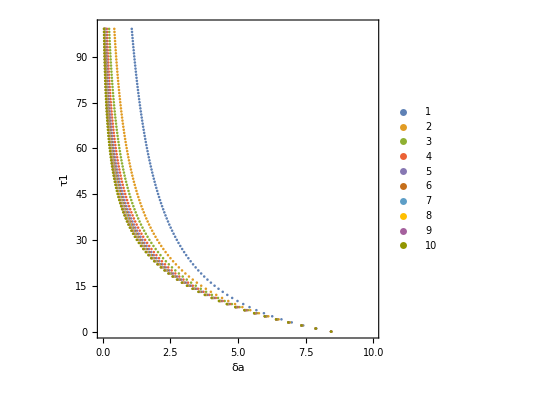

```mathematica
LimEqLCTn[t1_,n_] := δa/.Solve[q(fJ)^n == δa, δa][[1]]/.{q->qq, δj -> δjq, A0->A0q, n->nn, τ1->t1};

DDEplot = ListLinePlot[
Table[{daLimNT[τ1]/.{q->qq, δj -> δjq, A0->A0q}, τ1},{τ1, 0.1,100}]//Evaluate,
ImageSize->{400,400},
AspectRatio-> 1,
Frame -> True,
FrameTicks -> {{Automatic, None}, {Automatic, None}}, 
FrameLabel -> {"δa", "τ1"},
PlotStyle->{Thick, Red},
PlotRange->{{0,10},{0,100}}
];

ODEplot = ListLinePlot[
Table[{LimEqODE[τ1]/.{q->qq, δj -> δjq, A0->A0q}, τ1},{τ1, 0.1,100}]//Evaluate,
ImageSize->{400,400},
AspectRatio-> 1,
Frame -> True,
FrameTicks -> {{Automatic, None}, {Automatic, None}}, 
FrameLabel -> {"δa", "τ1"},
PlotStyle->{Thick, Blue},
PlotRange->{{0,10},{0,100}}
];

LCTplots = ListPlot[
Table[Table[{LimEqLCTn[1,n], τ1},{τ1, 0.1,100}],{n,1,10}]//Evaluate,
ImageSize->{400,400},
AspectRatio-> 1,
Frame -> True,
FrameTicks -> {{Automatic, None}, {Automatic, None}}, 
FrameLabel -> {"δa", "τ1"},
PlotLegends->Table[n, {n,1,10}],
PlotRange->{{0,10},{0,100}}
];

Show[DDEplot, ODEplot, LCTplots]
```

## Diagramme de stabilité fonction de δa et τ1

Pour des paramètres + liés à Gurney 1983 - Nicholson’s blowflies mais avec une mortalité juvénile boostée:

```mathematica
VPMaxLCT1[da_, t1_] := Eigenvalues[lJeqNonTriLCT/.{δa->da, τ1->t1}/.parTable1/.{n->nn}] //Re // Max;
table1 = Table[{δa, τ1, VPMaxLCT1[δa, τ1]},{δa, 0.01,1,0.02},{τ1, 0.01,50,1}];
table1flat = Flatten[table1,1]; (* Flatten first and second dimension -> have a list of triplets*)

StabContourPlot = ListContourPlot[table1flat,
ImageSize->{400,400},
AspectRatio-> 1,
Frame->{{True,False},{True,False}},
Axes->False,
FrameLabel-> {"δa", "τ1"},
Contours->{0},(*Trace la courbe Re(λ)=0*)
ContourStyle->{Thick,Black},
ColorFunction->(If[#>0,Purple,Yellow]&),
ColorFunctionScaling->False,
PlotLabel->"Régions de stabilité (jaune-stable)",
PlotRange->{{0,1},{0,50}}
];

RegionPlotExLCT = RegionPlot[CondInexLCT/.parTable1/.n->nn, 
{δa, 0, 1}, {τ1, 0, 50},
ImageSize->{400,400},
AspectRatio-> 1,
Frame -> False,
Axes -> True,
AxesLabel-> {"δa", "τ1"},
ColorFunction->Hue
];

stabcurveLCT = ParametricPlot[{LimEqLCT[τ1]/.parTable1/.n->nn, τ1}, 
{τ1, 0.1,50},
ImageSize->{400,400},
AspectRatio-> 1,
Frame -> True,
FrameTicks -> {{Automatic, None}, {Automatic, None}}, 
PlotLegends -> Automatic, 
PlotStyle->{Thick,Red},
FrameLabel -> {"δa", "τ1"},
PlotRange->{{0,10},{0,100}}
];

Show[StabContourPlot, RegionPlotExLCT,stabcurveLCT]
```

-Graphics-

Et si on prend les paramètres de Plodia :

```mathematica
parTablePlodia = {δj -> 0.,q-> 9.4, A0->15};
VPMaxLCT1[da_, t1_] := Eigenvalues[lJeqNonTriLCT/.{δa->da, τ1->t1}/.parTablePlodia/.{n->nn}] //Re // Max;
table1 = Table[{δa, τ1, VPMaxLCT1[δa, τ1]},{δa, 0.01,1,0.02},{τ1, 0.01,50,1}];
table1flat = Flatten[table1,1]; (* Flatten first and second dimension -> have a list of triplets*)

StabContourPlot = ListContourPlot[table1flat,
ImageSize->{400,400},
AspectRatio-> 1,
Frame->{{True,False},{True,False}},
Axes->False,
FrameLabel-> {"δa", "τ1"},
Contours->{0},(*Trace la courbe Re(λ)=0*)
ContourStyle->{Thick,Black},
ColorFunction->(If[#>0,Purple,Yellow]&),
ColorFunctionScaling->False,
PlotLabel->"Régions de stabilité (jaune-stable)",
PlotRange->{{0,1},{0,50}}
];

RegionPlotExLCT = RegionPlot[CondInexLCT/.parTable1/.n->nn, 
{δa, 0, 1}, {τ1, 0, 50},
ImageSize->{400,400},
AspectRatio-> 1,
Frame -> False,
Axes -> True,
AxesLabel-> {"δa", "τ1"},
ColorFunction->Hue
];

stabcurveLCT = ParametricPlot[{LimEqLCT[τ1]/.parTable1/.n->nn, τ1}, 
{τ1, 0.1,50},
ImageSize->{400,400},
AspectRatio-> 1,
Frame -> True,
FrameTicks -> {{Automatic, None}, {Automatic, None}}, 
PlotLegends -> Automatic, 
PlotStyle->{Thick,Red},
FrameLabel -> {"δa", "τ1"},
PlotRange->{{0,10},{0,100}}
];

Show[StabContourPlot, RegionPlotExLCT,stabcurveLCT]
```

-Graphics-

La mortalité intrinsèque juvénile considérée nulle pour Plodia dans Gurney 1983 déstabilise fortement le système et crée/agrandit la patate.

## Dynamiques LCT

```mathematica
tmax = 1000;
parInstable = {δa->0.15, τ1->12, q->8.5, A0->600, δj->0.07};
parStable = {δa->0.5, τ1->25, q->8.5, A0->600, δj->0.07};
parLimite = {δa->0.1, τ1->20, q->8.5, A0->600, δj->0.07};
leqnICLCT = Flatten[{systemLCT, {J[1][0] == 100, Table[J[i][0] == 100,{i,2,nn}],A[0] == 0}}];
```

### Dans la “patate instable”

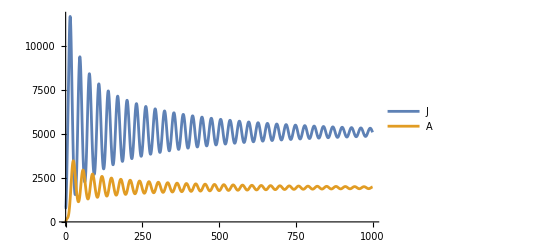

```mathematica
solPatate=NDSolve[leqnICLCT/.parInstable/.n->nn, {J[1], Table[J[i],{i,2,nn}],A}//Flatten,{t, 0,tmax}];
Plot[{J[t]/. solPatate[[1]]//Evaluate,A[t]/.solPatate[[1]]//Evaluate},{t,0,tmax},
PlotRange->Full,
PlotLegends->{"J", "A"}
]
```

NB : c’est pas des GC (T ~= 58 alors que τ1=12)

### Près de la limite

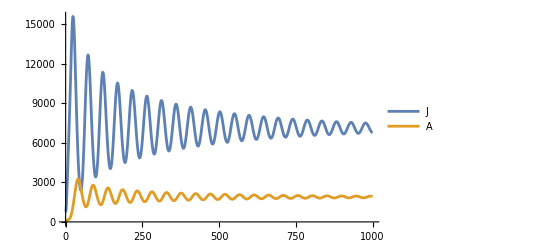

```mathematica
solLimite=NDSolve[leqnICLCT/.parLimite/.n->nn, {J[1], Table[J[i],{i,2,nn}],A}//Flatten,{t, 0,tmax}];
Plot[{J[t]/. solLimite[[1]]//Evaluate,A[t]/.solLimite[[1]]//Evaluate},{t,0,tmax},
PlotRange->Full,
PlotLegends->{"J", "A"}
]
```

### Dans la partie stable

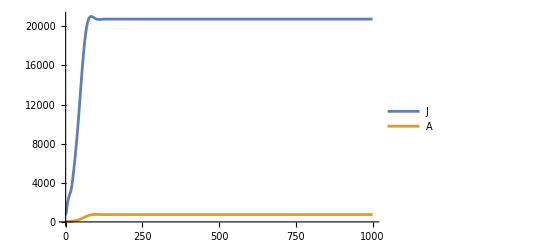

```mathematica
solStable=NDSolve[leqnICLCT/.parStable/.n->nn, {J[1], Table[J[i],{i,2,nn}],A}//Flatten,{t, 0,tmax}];
Plot[{J[t]/. solStable[[1]]//Evaluate,A[t]/.solStable[[1]]//Evaluate},{t,0,tmax},
PlotRange->Full,
PlotLegends->{"J", "A"}
]
```

## Comparaison dynamiques dans la patate (δj = 0.07) selon la variabilité développementale

```mathematica
tmax = 1000;
parInstable = {δa->0.15, τ1->12, q->8.5, A0->600, δj->0.07};

leqnICLCT = Flatten[{systemLCT, {J[1][0] == 100, Table[J[i][0] == 100,{i,2,nn}],A[0] == A0/.parInstable}}];

systemMinDDE= {
A'[t] == q A[t-τ1]Exp[-A[t-τ1]/A0] Exp[-δj τ1]  - δa A[t]};
leqnICDDE=Flatten[{systemMinDDE,{A[t/;t<=0]==A0/.parInstable}}];

systemODE ={
Jode'[t] == q A[t] Exp[-A[t]/A0] - Jode[t]/τ1 - δj Jode[t], 
A'[t] == Jode[t]/τ1 - δa A[t]};
leqnICODE = Flatten[{systemODE, {Jode[0] == 10,A[0] == A0/.parInstable}}];
```

```mathematica
solDDE=NDSolve[leqnICDDE/. parInstable,{A},{t,0,tmax}];
solODE=NDSolve[leqnICODE/. parInstable,{Jode,A},{t,0,tmax}];
solLCT=NDSolve[leqnICLCT/.parInstable/.n->nn, {J[1], Table[J[i],{i,2,nn}],A}//Flatten,{t, 0,tmax}];
```

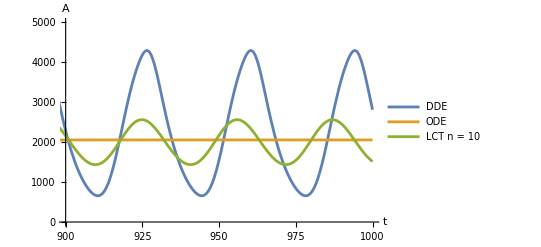

```mathematica
Plot[{A[t]/.solDDE[[1]]//Evaluate, A[t]/.solODE[[1]]//Evaluate, A[t]/.solLCT[[1]]//Evaluate},{t,0,tmax},
PlotRange->{{tmax-100, tmax},{0,5000}},
PlotLegends->{"DDE", "ODE", "LCT n = "<>ToString[nn]},
AxesLabel->{"t", "A"}
]
```

## Conclusion pour LCT

## Application des résultats analytiques de Beretta et Breda 2016

## Résultats du Beretta et Breda 2016

```mathematica
Clear[aB, bB, dB, d1B, ηB, τB, τ1B,n];
aBpar = 7;
bBpar = 350;
dBpar = 1;
d1Bpar = 0.25;
ηBpar = Log[bB/dB]/.{bB->bBpar, dB->dBpar} //N;
parBeretta = {aB->aBpar, bB->bBpar, dB -> dBpar, d1B->d1Bpar, ηB->ηBpar}
enB[z_] := (1+z/n)^n;
```

{aB→7,bB→350,dB→1,d1B→0.25,ηB→5.85793}

```mathematica
τplus = n/d1B(ⅇ^(ηB/n)-1);
τω = n/d1B(ⅇ^((ηB-2)/n)-1);
```

Trouver ω^(n)(τ) revient à trouver la racine d’un long polynôme de degré n dans le cas d’un délai distribué, puis de calculer sa racine carrée (équations 50-53).
Calculons là pour un τ général

```mathematica
Clear[ωn];
qB[ν_, τ_,n_] := (ν/(n+1-ν)+dB^2(τ/(n+d1B τ))^2) Binomial[n, ν] (τ/(n+ d1B τ))^(2(ν-1));
T[t_, τ_,n_] := -dB^2 * (ηB - Log[enB[d1B τ]])(ηB-Log[enB[d1B τ]] -2) +Sum[qB[ν, τ,n]*t^ν,{ν, 1,n,1}] + (τ/(n+d1B τ))^(2n)*t^(n+1);
ωn[τ_, par_,ni_] := Module[{polreplaced, troot, ωnresult},
polreplaced = T[t,τ,ni]/.par/.n->ni;
troot = t/.FindRoot[polreplaced == 0, {t,0.01}];
ωnresult = Sqrt[troot];
ωnresult]
ωn[5, parBeretta,10]
```

1.02545

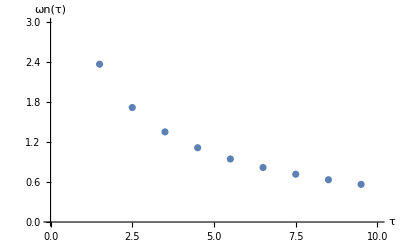

```mathematica
table = Table[{τ,ωn[τ, parBeretta,10]}, {τ,0.5,10,1}];
ListPlot[table, PlotRange->{{0,10},{0,3}},
AxesLabel->{"τ", "ωn(τ)"}]
```

Calculons ainsi la fonction ϕ^(n)(τ) qui devra traverser des multiples impairs strictement positifs de π pour l’existence d’une zone d’instabilité.

```mathematica
ϕ[τ_, par_, ni_] := ni ArcTan[(ωn[τ, par,ni]*τ)/(ni + d1B τ)] + ArcTan[ωn[τ, par,ni]/dB]/.par// N;
```

## Application : le jeu testé dans Beretta & Breda 2016

```mathematica
tplus = τplus/.parBeretta/.n->2
tω2 = τω/.parBeretta/.n->2
tplus = τplus/.parBeretta/.n->3
tω3 = τω/.parBeretta/.n->3
```

141.666

47.0592

72.5676

31.4184

```mathematica
d1dc =  ηB(ηB-1)(ηB-2);
d1dceg  = ηB(ηB-1)(ηB-2)/.parBeretta
d1deg = d1B/d1B/.parBeretta
d1deg < d1dceg
```

109.787

1

True

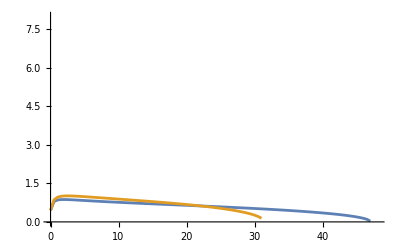

```mathematica
tableϕ = Table[Table[{τ, ϕ[τ, parBeretta,ntable]/Pi}, {τ,0.01,1+tω2, 0.5}],{ntable,2,3,1}];
Show[
ListLinePlot[tableϕ,
PlotRange->{{0,1+tω2},{0,8}}],
Prolog->{Dashed,Thickness[0.005],Table[Line[{{x,1},{x,1}}],{x,0,50,0.5}]}
]
```

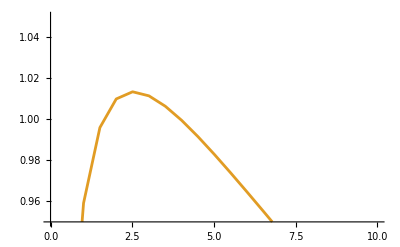

```mathematica
tableϕ = Table[Table[{τ, ϕ[τ, parBeretta,ntable]/Pi}, {τ,0.01,1+tω2, 0.5}],{ntable,2,3,1}];
Show[
ListLinePlot[tableϕ,
PlotRange->{{0,10},{0.95,1.05}}],
Prolog->{Dashed,Thickness[0.005],Table[Line[{{x,1},{x,1}}],{x,0,50,0.5}]}
]
```

Ok pour les limites de la patate mais le reste de la fonction semble différer de ce qu’on voit dans la figure 4 de Beretta2016.

FindRoot::lstol: The line search decreased the step size to within tolerance specified by AccuracyGoal and PrecisionGoal but was unable to find a sufficient decrease in the merit function. You may need more than MachinePrecision digits of working precision to meet these tolerances.

General::munfl: 1.78118×10^-239 1.×10^-70 is too small to represent as a normalized machine number; precision may be lost.

General::munfl: 1.11506×10^-247 1.×10^-72 is too small to represent as a normalized machine number; precision may be lost.

General::munfl: 4.52444×10^-256 1.×10^-74 is too small to represent as a normalized machine number; precision may be lost.

General::stop: Further output of General::munfl will be suppressed during this calculation.

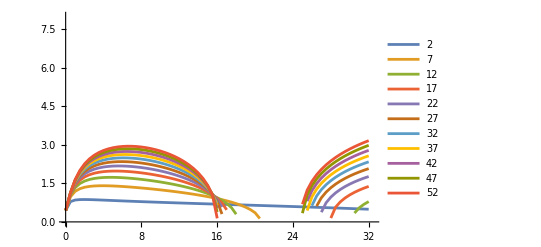

```mathematica
tableϕ = Table[Table[{τ, ϕ[τ, parBeretta,ntable]/Pi}, {τ,0.01,1+tω3, 0.5}],{ntable,2,53,5}];
Show[
ListLinePlot[tableϕ,
PlotRange->{{0,1+tω3},{0,8}},
PlotLegends->Table[n,{n,2,53,5}]],
Prolog->{Dashed,Thickness[0.005],Table[Line[{{x,1},{x,1}}],{x,0,50,0.5}]}
]
```

## Application : deux jeux de paramètres inspirés de Gurney 1983 : Quentin, Plodia ventura

### Identification des deux modèles

Pour rappel, on considérait l’équation:
	A’[t] == q A[t - τ1 ] Exp[-A[t - τ1]/A0] Exp[-δj τ1]  - δa A[t]
Correspondance des paramètres : on se rapport à l’équation (2) de Beretta & Breda 2016.
	a_Beretta = 1/N_0
	b_Beretta = q
	d1_Beretta = δj
	d_Beretta = δa
	τ_Beretta = τ1

```mathematica
aB  = 1/A0;
bB = q;
d1B = δj;
dB= δa;
τB = τ1;
ηB = Log[bB/dB];
```

Rappel : sous LCT, 
	EqNTMathis = A0*Log[q/δa(fJ)^n] // FullSimplify

```mathematica
enB[z_] := (1+z/n)^n;
EqNT = (ηB - Log[enB[d1B τB]])/aB
```

```mathematica
fJ = θ/(θ+δj);
EqNTMathis=A0*Log[q/δa(fJ)^n] /. θ->n/τ1 // FullSimplify
```

A0 Log[(q (n/(n+δj τ1))^n)/δa]

Fusionner les deux log dans l’expression du haut montre que ces deux expressions sont égales.

```mathematica
d1dc // FullSimplify
d1d = d1B/dB //FullSimplify
```

(-2+Log[q/δa]) (-1+Log[q/δa]) Log[q/δa]

δj/δa

Cela revient à vérifier que δj/δa < ln(ρ)(ln(ρ)-1)(ln(ρ)-2))
-> On imagine mieux pourquoi augmenter écrire δj = 0 augmente énormément la taille de la patate : ici cela voudrait dire que la patate existe toujours tant que ρ > 1( certes ça ne donne pas d’info sur sa taille)
-> On voit aussi comme le terme de gauche est > 0 que on doit avoir ln(ρ)>2 ie q > ⅇ^2 δa soit environ 7.4 δa

```mathematica
ⅇ^2//N
```

7.38906

### Paramètres utilisés par Gurney

```mathematica
qq=8.5;
δaq=0.27;
δjq=0.07;
τ1q=0.6;
A0q=600;
parQuentin = {q->qq, δa-> δaq, δj -> δjq, τ1->τ1q, A0->A0q};
ntest = 20;

parPlodia =  {q-> 9.4, δa->0.2, δj -> 0.,τ1-> 28, q-> 9.4, A0->15};
```

```mathematica
τplus /.parQuentinwotau/.n->ntest
τω/.parQuentinwotau/.n->ntest
```

57.8784

22.1318

```mathematica
parQuentinwotau =  {q->qq, δa-> δaq, δj -> δjq, A0->A0q};
tableϕ = Table[{τ, ϕ[τ, parQuentinwotau,ntest]/Pi}, {τ,0.01,τω/.parQuentinwotau/.n->ntest, 1}];
Show[
ListLinePlot[tableϕ,
PlotRange->{{0,τω/.parQuentinwotau/.n->ntest},{0,1.5}}],
Prolog->{Full,Thickness[0.005],Table[Line[{{x,1},{x,1}}],{x,0,50,0.1}]}
]
```

-Graphics-

```mathematica
bigtableϕ = Table[Table[{τ, ϕ[τ, parQuentinwotau,ni]/Pi}, {τ,0.01,τω/.parQuentinwotau/.n->ni, 1}], {ni,5,15,1}];
```

```mathematica
Show[
ListLinePlot[bigtableϕ,
ImageSize->800,
PlotRange->{{0,25},{0,1.5}},
PlotLegends->nvect],
Prolog->{Full,Thickness[0.005],Table[Line[{{x,1},{x,1}}],{x,0,50,0.1}]}
]
```

-Graphics-

Et en appliquant les résultats calculés pour le cadre délai fixe:

```mathematica
nvect = {1,5,10,15,20,30,40,50,75};
bigtableϕ = Table[Table[{τ, ϕ[τ, parQuentinwotau,ni]/Pi}, {τ,0.01,τω/.parQuentinwotau/.n->ni, 1}], {ni,nvect}];
Show[
ListLinePlot[bigtableϕ,
ImageSize->800,
PlotRange->{{0,25},{0,1.5}},
PlotLegends->nvect],
Prolog->{Full,Thickness[0.005],Table[Line[{{x,1},{x,1}}],{x,0,50,0.1}]}
]
```

General::munfl: 6.83271×10^-289 1.×10^-82 is too small to represent as a normalized machine number; precision may be lost.

General::munfl: 1.×10^-200 1.26588×10^-170 is too small to represent as a normalized machine number; precision may be lost.

General::stop: Further output of General::munfl will be suppressed during this calculation.

FindRoot::nlnum: The function value {False} is not a list of numbers with dimensions {1} at {t} = {0.01}.

ReplaceAll::reps: {FindRoot[polreplaced$251847==0,{t,0.01}]} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

FindRoot::nlnum: The function value {False} is not a list of numbers with dimensions {1} at {t} = {0.01}.

ReplaceAll::reps: {FindRoot[polreplaced$251847==0,{t,0.01}]} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

FindRoot::nlnum: The function value {False} is not a list of numbers with dimensions {1} at {t} = {0.01}.

General::stop: Further output of FindRoot::nlnum will be suppressed during this calculation.

ReplaceAll::reps: {FindRoot[polreplaced$251847==0,{t,0.01}]} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

General::stop: Further output of ReplaceAll::reps will be suppressed during this calculation.

FindRoot::lstol: The line search decreased the step size to within tolerance specified by AccuracyGoal and PrecisionGoal but was unable to find a sufficient decrease in the merit function. You may need more than MachinePrecision digits of working precision to meet these tolerances.

General::stop: Further output of FindRoot::lstol will be suppressed during this calculation.

FindRoot::jsing: Encountered a singular Jacobian at the point {t} = {0.01}. Try perturbing the initial point(s).

General::stop: Further output of FindRoot::jsing will be suppressed during this calculation.

FindRoot::nlnum: The function value {False} is not a list of numbers with dimensions {1} at {t} = {0.01}.

ReplaceAll::reps: {FindRoot[polreplaced$251847==0.,{t,0.01}]} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

FindRoot::nlnum: The function value {False} is not a list of numbers with dimensions {1} at {t} = {0.01}.

ReplaceAll::reps: {FindRoot[polreplaced$251869==0.,{t,0.01}]} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

FindRoot::nlnum: The function value {False} is not a list of numbers with dimensions {1} at {t} = {0.01}.

General::stop: Further output of FindRoot::nlnum will be suppressed during this calculation.

ReplaceAll::reps: {FindRoot[polreplaced$251959==0.,{t,0.01}]} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

General::stop: Further output of ReplaceAll::reps will be suppressed during this calculation.

-Graphics-